### Preliminary AUC calculation

#### Phase Space Metric

```mathematica
Clear[heavidandϵ]
dofxs[z_,zp_,s_:mW^2,sp_:mW^2]:= 2(s+sp) - 4 Min[z (1-z),zp(1-zp)] √(s/(z(1-z)) sp/(zp(1-zp)))(*from appendix of smeared likelihood paper*)

heavidandϵ[ϵ_?NumericQ,z_?NumericQ,zp_?NumericQ]:=HeavisideTheta[ϵ -√( 4 (1 -If[z(1-z)>zp(1-zp), √((zp(1-zp))/(z (1-z))) ,√((z(1-z))/(zp (1-zp)))]))](* ϵ in units of mW - assumes s = s' = Subscript[m, W]^2*)
```

#### Smeared Phase Space Distributions

```mathematica
Clear[psignal,pquark,pgluon]

(*domain of integration is broken up for convergence (otherwise mathematica thinks it's 0)*)

psignal[z_?NumberQ,ϵ_?NumberQ]:=Quiet@Total@(NIntegrate[3/2 (zp^2+(1-zp)^2)heavidandϵ[ϵ,z,zp],{zp,#[[1]],#[[2]]}]&/@{{0,0.5},{0.5,1}})(*we calculated this splitting function, for W -> ff' *)

pquark[z_?NumberQ,ϵ_?NumberQ,pp_:10/R]:=Quiet@Total@(NIntegrate[ ((1+(1-z)^2)/z+(1+z^2)/(1-z))/(2 Log[R^2 pp^2//Simplify]-3/2)heavidandϵ[ϵ,z,zp],{zp,#[[1]],#[[2]]}]&/@{{0,0.5},{0.5,1}})(*pp in units of mW - from Andrew's H->gg likelihood paper*)

pgluon[z_?NumberQ,ϵ_?NumberQ,pp_:10/R]:=Quiet@Total@(NIntegrate[ (CA (zp/(1-zp)+(1-zp)/zp+zp(1-zp)) + nf TR (zp^2+(1-zp)^2))/(2 CA Log[R^2 pp^2//Simplify]- 11/6 CA + 2/3 nf TR)heavidandϵ[ϵ,z,zp]/. {CA -> 3,CF->4/3,nf -> 3, TR->1/2 },{zp,#[[1]],#[[2]]}]&/@{{0,0.5},{0.5,1}})(*pp in units of mW - pp >> mW and is farily irrelevant since in only changes a constant prefactor of the CDF*)
```

```mathematica
"Interpolate the distributions"
psignalf=Interpolation[Table[{z,psignal[z,1]},{z,0.01,0.99,0.01}]]
pquarkf=Interpolation[Table[{z,pquark[z,1]},{z,0.01,0.99,0.01}]]
pgluonf=Interpolation[Table[{z,pgluon[z,1]},{z,0.01,0.99,0.01}]]
```

Interpolate the distributions

InterpolatingFunction[…]

InterpolatingFunction[…]

InterpolatingFunction[…]

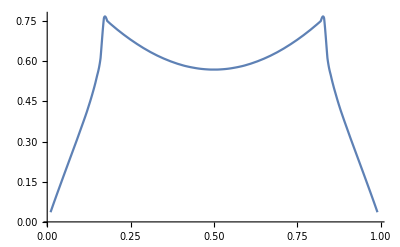

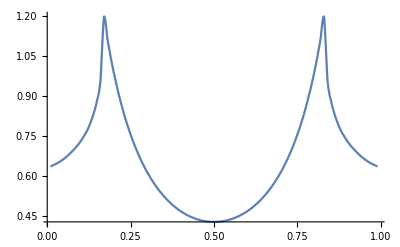

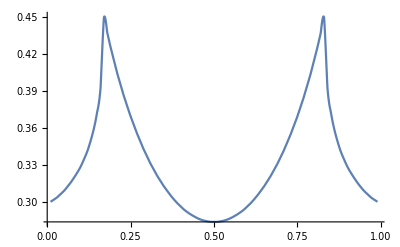

```mathematica
Plot[psignalf[z],{z,psignalf["Domain"][[1,1]],psignalf["Domain"][[1,2]]}]
Plot[pquarkf[zp],{zp,pquarkf["Domain"][[1,1]],pquarkf["Domain"][[1,2]]}]
Plot[pgluonf[zp],{zp,pgluonf["Domain"][[1,1]],pgluonf["Domain"][[1,2]]}]
```

#### Phase Space distance CDF (quark and gluon background separately)

```mathematica
Clear[AUCqW]
AUCqW[d_?NumericQ]:= NIntegrate[psignalf[z]pquarkf[zp] heavidandϵ[d,z,zp],{z,psignalf["Domain"][[1,1]],psignalf["Domain"][[1,2]]},{zp,pquarkf["Domain"][[1,1]],pquarkf["Domain"][[1,2]]},PrecisionGoal->5,AccuracyGoal->5,Method->"LocalAdaptive"]

AUCgW[d_?NumericQ]:= NIntegrate[psignalf[z]pgluonf[zp] heavidandϵ[d,z,zp],{z,psignalf["Domain"][[1,1]],psignalf["Domain"][[1,2]]},{zp,pgluonf["Domain"][[1,1]],pgluonf["Domain"][[1,2]]},PrecisionGoal->5,AccuracyGoal->5,Method->"LocalAdaptive"]
```

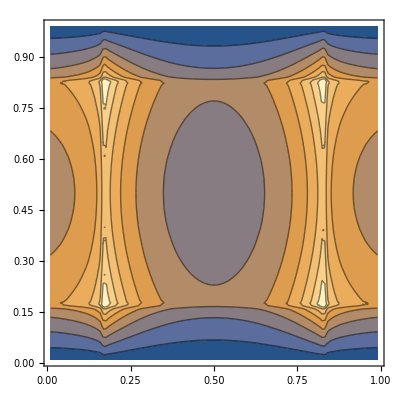

```mathematica
ContourPlot[pquarkf[zp]psignalf[z]heavidandϵ[4,z,zp],{zp,pquarkf["Domain"][[1,1]],pquarkf["Domain"][[1,2]]},{z,psignalf["Domain"][[1,1]],psignalf["Domain"][[1,2]]}]
```

```mathematica
"Interpolate the CDF in d for gluon and quark background - As andrew outlined in the H->gg paper, in general the background distribution will be some linear combination of the two. So these two cases define the endpoints of an interval describing the true background distribution.";

AUCqWtable=Table[{d,AUCqW[d]},{d,0.01,3,0.03}];
NormedAUCqWtable=Table[{AUCqWtable[[i,1]],AUCqWtable[[i,2]]/Max[AUCqWtable[[;;,2]]]},{i,Length[AUCqWtable]}];

AUCgWtable=Table[{d,AUCgW[d]},{d,0.01,3,0.03}];
NormedAUCgWtable=Table[{AUCgWtable[[i,1]],AUCgWtable[[i,2]]/Max[AUCgWtable[[;;,2]]]},{i,Length[AUCgWtable]}];
```

#### Plot the CDFs (and fit to parabolas)

0.00629337+0.970957 d^2

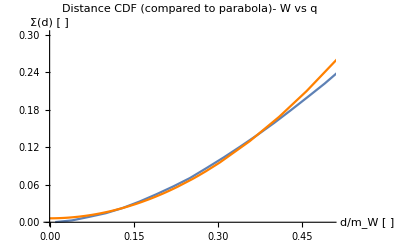

```mathematica
smalldfitfunc=Fit[NormedAUCqWtable[[;;15]],{1,d^2},{d}]
Show[{ListLinePlot[NormedAUCqWtable,AxesLabel->{"d/m_W [ ]","Σ(d) [ ]"},PlotLabel->"Distance CDF (compared to parabola)- W vs q",PlotRange->{{0,0.5},{0,0.3}}],Plot[smalldfitfunc,{d,0,2.5},PlotStyle->Orange]}]
```

0.00629337+0.970957 d^2

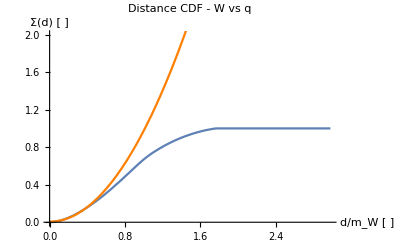

```mathematica
smalldfitfunc=Fit[NormedAUCqWtable[[;;15]],{1,d^2},{d}]
Show[{ListLinePlot[NormedAUCqWtable,AxesLabel->{"d/m_W [ ]","Σ(d) [ ]"},PlotLabel->"Distance CDF - W vs q",PlotRange->{0,2}],Plot[smalldfitfunc,{d,0,2.5},PlotStyle->Orange]}]
```

0.00858511+1.07973 d^2

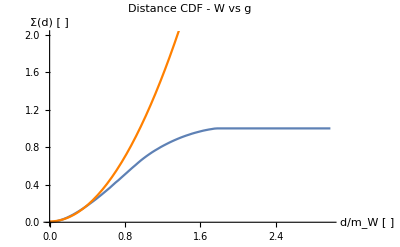

```mathematica
smalldfitfunc=Fit[NormedAUCgWtable[[;;15]],{1,d^2},{d}]
Show[{ListLinePlot[NormedAUCgWtable,AxesLabel->{"d/m_W [ ]","Σ(d) [ ]"},PlotRange->{0,2},PlotLabel->"Distance CDF - W vs g"],Plot[smalldfitfunc,{d,0,2.5},PlotStyle->Orange]}]
```

The small d fits also show us that there is little difference between the q and g background at leading order.